## functions

```mathematica
runtm[rl_Integer,steps_:50]:=TuringMachine[{rl,4,4},{1,{{},0}},steps]
```

```mathematica
numtm[s_,k_]:=(2s k)^(s k)
```

```mathematica
randomtm[s_,k_]:=RandomInteger[{0,numtm[s,k]-1}]
```

```mathematica
CleanTM[evol_]:=Catch@Module[
{diffs,growthrate,growthdirection,rotate,rotatefactor,dy,dx,posdiffs},
diffs=Differences[evol];
posdiffs=Differences[Position[diffs,x_Integer/;x=!=0,{2}]];
If[posdiffs=={},Throw[evol]];
{dx,dy}=Mean/@Transpose@posdiffs;
growthrate=If[dx=!=0,dy/dx,0];
growthdirection=Sign@growthrate;
rotate=If[growthdirection<0,RotateRight,RotateLeft];
rotatefactor=Abs[growthrate];
MapIndexed[rotate[#,Round[#2[[1]]*rotatefactor]]&,diffs]
]
```

Number of distinct run lengths:

```mathematica
firstmoment[headpos_]:=Length@Tally[Length/@Split@Differences@headpos]
```

Number of distinct run length frequencies:

```mathematica
secondmoment[headpos_]:=Length@Tally[Length/@Gather@Tally[Sort[Length/@Split@Differences@headpos]][[All,-1]]]
```

```mathematica
moments[headpos_List]:={firstmoment[headpos],secondmoment[headpos]}
```

```mathematica
tmrule[numstates_,numcolors_,rnum_]:=Sort[With[{s=numstates,k=numcolors,n=rnum},Flatten[MapIndexed[{1,-1} #2+{0,k}->{1,1,2} Mod[Quotient[#1,{2 k,2,1}],{s,k,2}]+{1,0,-1}&,Partition[IntegerDigits[n,2 s k,s k],k],{2}]]]]
```

```mathematica
rightcompress[evol_List]:=Module[{maxright=evol[[1,1,2]]},
Reap[
If[
#[[1,2]]>maxright,
maxright=#[[1,2]];Sow[#]
]&/@evol
][[2,1]]
]
```

```mathematica
leftcompress[evol_List]:=Module[{maxleft=evol[[1,1,2]]},
Reap[
If[
#[[1,2]]<maxleft,
maxleft=#[[1,2]];Sow[#]
]&/@evol
][[2,1]]
]
```

## super simple

```mathematica
evol=runtm[565126726677701498333035];
```

```mathematica
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]],PixelConstrained->2]
```

-Graphics-

```mathematica
ListLinePlot[headpos,ImageSize->100]
```

-Graphics-

There is only one distinct run length:

```mathematica
firstmoment@headpos
```

1

... and therefore only one distinct run length frequency:

```mathematica
secondmoment@headpos
```

1

## repetitive

```mathematica
evol=runtm[696321785753216365840842,200];
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]],PixelConstrained->2]
```

-Graphics-

```mathematica
ArrayPlot[leftcompress[evol][[All,2]],ImageSize->100]
```

-Graphics-

```mathematica
ArrayPlot[rightcompress[evol][[All,2]],ImageSize->100]
```

-Graphics-

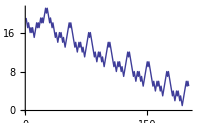

```mathematica
ListLinePlot[headpos,ImageSize->200]
```

```mathematica
firstmoment[headpos]
```

4

```mathematica
secondmoment[headpos]
```

1

```mathematica
994010225841132990505891
```

```mathematica
evol=runtm[994010225841132990505891,200];
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]],PixelConstrained->2]
```

-Graphics-

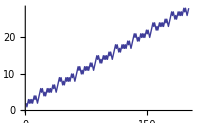

```mathematica
ListLinePlot[headpos,ImageSize->200]
```

```mathematica
firstmoment[headpos]
```

3

```mathematica
secondmoment[headpos]
```

1

## nested

```mathematica
241087253459803902428208
```

```mathematica
evol=runtm[241087253459803902428208,200];
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]],PixelConstrained->2]
```

-Graphics-

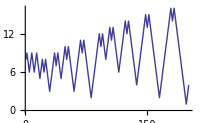

```mathematica
ListLinePlot[headpos,ImageSize->200]
```

```mathematica
firstmoment[headpos]
```

14

```mathematica
secondmoment[headpos]
```

4

```mathematica
190245539805998439072866
```

```mathematica
evol=runtm[190245539805998439072866,200];
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]],PixelConstrained->2]
```

-Graphics-

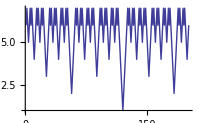

```mathematica
ListLinePlot[headpos,ImageSize->200]
```

```mathematica
firstmoment[headpos]
```

6

```mathematica
secondmoment[headpos]
```

1

```mathematica
771921737758066372850424
```

```mathematica
evol=runtm[771921737758066372850424,200];
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]],PixelConstrained->2]
```

-Graphics-

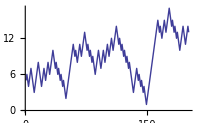

```mathematica
ListLinePlot[headpos,ImageSize->200]
```

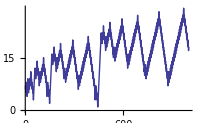

```mathematica
ListLinePlot[runtm[771921737758066372850424,1000][[All,1,2]],ImageSize->200]
```

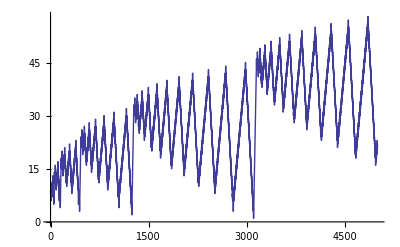

```mathematica
ListLinePlot[runtm[771921737758066372850424,5000][[All,1,2]],ImageSize->400]
```

```mathematica
firstmoment[runtm[771921737758066372850424,5000][[All,1,2]]]
```

10

```mathematica
secondmoment[runtm[771921737758066372850424,5000][[All,1,2]]]
```

2

```mathematica
391023735294262233647299
```

```mathematica
evol=runtm[391023735294262233647299,200];
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]],PixelConstrained->2]
```

-Graphics-

```mathematica
headpos=runtm[391023735294262233647299,2000][[All,1,2]];
```

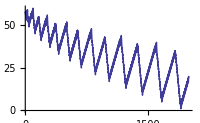

```mathematica
ListLinePlot[headpos,ImageSize->200]
```

```mathematica
firstmoment@headpos
```

6

```mathematica
secondmoment@headpos
```

1

## search

```mathematica
i=0;
kept1={};
kept2={};
outfile=FileNameJoin[{NotebookDirectory[],"tm-4-4-search.txt"}];
```

```mathematica
DynamicModule[
{runQ=False},
Dynamic@Column[{
Row[{"run: ",Checkbox[Dynamic[runQ],Appearance->Large]," ---> ",Dynamic@runQ}," "],
Switch[runQ,
True,
Refresh[Module[
{rl = randomtm[4, 4], plot, evol, cleanplot, steps = 25,imoments},
If[Length@Union@CleanTM[Last /@ TuringMachine[{rl, 4, 4}, {{1, steps}, Table[0, {2*steps}]}, steps]]/steps > 0.5, 
Sow@rl;
AppendTo[kept1,rl];
evol=runtm[rl,1000];
imoments=moments[evol];
If[imoments[[2]]>1&&imoments[[1]]>5,
AppendTo[kept2,{rl,imoments}];
PutAppend[{rl,imoments},outfile]
]
];
i++
],TrackedSymbols->{i}],
False,
i
],
Row[{"i=",i,,", kept stage 1: ",Length@kept1,", kept stage 2: ",Length@kept2}]
}
]
]
```

```mathematica
keep={};
Dynamic@Grid[Partition[Table[Module[
{plot,evol,cleanplot,rnum=rl[[1]],m=rl[[2]]},
evol=TuringMachine[{rnum,4,4},{{1,50},Table[0,{100}]},50];
plot=ArrayPlot[Last/@evol,PixelConstrained->2,Frame->None];
With[{r=rnum,im=m},Tooltip[Button[plot,AppendTo[keep,{plot,r}],Appearance->None],Dynamic@Labeled[ArrayPlot[runtm[r,200][[All,2]],PixelConstrained->2],im,Top]]]
],{rl,kept2}],3,3,1,{}],Frame->All,FrameStyle->LightGray]
```

```mathematica
kept2=ReadList[FileNameJoin[{NotebookDirectory[],"tm-4-4-search.txt"}],Expression];
```

```mathematica
kept2
```

{{1093336516567299391842147,{13,2}},{224459642189002768599678,{11,2}},{573571293230444984038756,{34,2}},{895256078473522558356204,{11,2}},{1013773378631864051290804,{12,2}},{909842690785677294918999,{13,2}},{212347912419135721184650,{23,3}},{224642690893523584558313,{16,2}},{394935456286726931056356,{13,2}},{304165244211879220272757,{16,2}},{330371094342539502164819,{21,2}},{562274249328608565715338,{12,2}},{652313450225507668436110,{13,2}},{563637183082375546919786,{17,3}},{282003914349654358162961,{19,2}},{248503568824129848132559,{15,2}},{208593718385379384572724,{12,2}},{409248049335216719230765,{13,3}},{243164563628029711358543,{13,2}},{37812861021632658533613,{16,2}},{786046133060555216208777,{16,2}},{300855639267676866202418,{11,2}},{950945264741805312648918,{16,2}},{385552483735352930948614,{29,3}},{501959088040811291930638,{31,3}},{44508310584335868194886,{19,4}},{1174816999818430844945003,{17,2}},{709952950407716662248262,{8,2}},{613092662789187509759814,{16,3}},{79300510765381554870028,{29,3}},{263920325809125645851176,{10,3}},{643854170937830579066117,{6,2}},{314034650145681771548484,{6,2}},{48095000354701799024685,{15,2}},{166254421362516798956391,{12,2}},{871679324421646336194476,{22,2}},{453119357946800128488758,{6,2}},{879079407860393048331235,{6,2}},{239096966731190976358360,{28,2}},{1174927188690208254238949,{7,2}},{66323628268298262067783,{8,2}},{743943864582762873052346,{19,2}},{116858842528613395285617,{17,2}},{495465071220821534360301,{18,2}},{962723806345834610521524,{7,2}},{512798120344375503470718,{11,3}},{795712579832546234171015,{18,2}},{988374713744784137221100,{12,2}},{601759401803772438867465,{13,2}},{304566675379886352033231,{16,2}},{948632508973126906687334,{7,3}},{269153119963761120539206,{17,3}},{442674163099688764602213,{11,2}},{1108712292630336507941446,{15,2}},{355146150737288454957205,{11,2}},{421616210515025023994250,{25,2}},{1045022407525789248505991,{32,2}},{735603360054663689222036,{8,2}},{752749191142260377223492,{14,2}},{1010475110530355375832618,{8,2}},{824223817941757515115801,{13,2}},{715689452934078358779691,{17,2}}}

```mathematica
keep={};
```

```mathematica
Grid[Partition[Table[Module[
{plot,evol,cleanplot,rnum=rl[[1]],m=rl[[2]]},
evol=TuringMachine[{rnum,4,4},{{1,50},Table[0,{100}]},50];
plot=ArrayPlot[Last/@evol,PixelConstrained->2,Frame->None];
With[{r=rnum,im=m},Tooltip[Button[plot,AppendTo[keep,{plot,r}],Appearance->None],Dynamic@Labeled[ArrayPlot[runtm[r,200][[All,2]],PixelConstrained->2],im,Top]]]
],{rl,kept2}],3,3,1,{}],Frame->All,FrameStyle->LightGray]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
kept2[[1]]
```

{1093336516567299391842147,{13,2}}

```mathematica
Take[Reverse@SortBy[kept2,Total@#[[2]]&],10]
```

{{573571293230444984038756,{34,2}},{1045022407525789248505991,{32,2}},{501959088040811291930638,{31,3}},{385552483735352930948614,{29,3}},{79300510765381554870028,{29,3}},{239096966731190976358360,{28,2}},{421616210515025023994250,{25,2}},{212347912419135721184650,{23,3}},{871679324421646336194476,{22,2}},{330371094342539502164819,{21,2}}}

```mathematica
Grid[Partition[Table[Module[
{plot,evol,cleanplot,rnum=rl[[1]],m=rl[[2]]},
evol=TuringMachine[{rnum,4,4},{{1,50},Table[0,{100}]},50];
plot=ArrayPlot[Last/@evol,PixelConstrained->2,Frame->None];
With[{r=rnum,im=m},Tooltip[Button[plot,AppendTo[keep,{plot,r}],Appearance->None],Dynamic@Labeled[ArrayPlot[runtm[r,200][[All,2]],PixelConstrained->2],im,Top]]]
],{rl,Take[Reverse@SortBy[kept2,Total@#[[2]]&],10]}],3,3,1,{}],Frame->All,FrameStyle->LightGray]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
Dynamic[keep]
```

```mathematica
Clear[tmplot]
```

```mathematica
tmplot[rnum_,steps_:50,opts:OptionsPattern[ArrayPlot]]:=With[{evol=TuringMachine[{rnum,4,4},{{1,steps},Table[0,{2*steps}]},steps]},ArrayPlot[evol[[All,2]],opts,PixelConstrained->1]]
```

```mathematica
tmplot[501959088040811291930638,300,PixelConstrained->1]
```

-Graphics-

```mathematica
tmplot[1010475110530355375832618,300,PixelConstrained->1]
```

-Graphics-

```mathematica
ArrayPlot[TuringMachine[{1010475110530355375832618,4,4},{{1,200},Table[0,{2*200}]},5000][[All,2]],PixelConstrained->1]
```

-Graphics-

```mathematica
ArrayPlot[rightcompress[TuringMachine[{501959088040811291930638,4,4},{{1,50},Table[0,{2*50}]},100000]][[All,2]]]
```

-Graphics-

```mathematica
keep[[-1]]
```

{-Graphics-,366119830562655292810303}

```mathematica
evol=runtm[366119830562655292810303,500];
headpos=evol[[All,1,2]];
```

```mathematica
ArrayPlot[evol[[All,2]]]
```

-Graphics-

## tests

```mathematica
j=0;
DynamicModule[
{runQ=False},

Dynamic@Column[{
Row[{"run: ",Checkbox[Dynamic[runQ],Appearance->Large]," ---> ",runQ}," "],
Switch[runQ,True,Refresh[j++,TrackedSymbols->{j}],False,j]
}]

]
```